# Physics through Computational Thinking Week-7: Monte Carlo Simulation

Monte Carlo methods are computational algorithms that rely on repeated random sampling to obtain numerical results. In this tutorial, we learn the basics of Monte Carlo simulation using Mathematica.

## 1. Some Necessary Commands

Monte Carlo simulations uses random numbers.

Generating Random Numbers

```mathematica
xmin=-1;
xmax=1;
```

```mathematica
RandomReal[{xmin,xmax}]
```

0.454792

```mathematica
RandomReal[{xmin,xmax},10]
```

{-0.0966998,0.0358728,0.64145,-0.460335,-0.28348,-0.409109,-0.288914,0.738983,-0.432609,-0.312573}

Loops

Two useful methods for doing iterative calculations in Mathematica. 
(i) Do loop : It works well for simple and  nested loops.
(ii) While loop: It is useful for complex loops.

```mathematica
Do[
f = 2x+3;
Print["f=",f],
{x,-1,1,1}
] (*1D loop*)
```

f=1

f=3

f=5

```mathematica
Do[
f = x*y;
Print["x*y=",f," x=",x," y=",y,"."],
{x,-1,1,1},{y,-1,1,1}
] (*2D loop*)
```

x*y=1 x=-1 y=-1.

x*y=0 x=-1 y=0.

x*y=-1 x=-1 y=1.

x*y=0 x=0 y=-1.

x*y=0 x=0 y=0.

x*y=0 x=0 y=1.

x*y=-1 x=1 y=-1.

x*y=0 x=1 y=0.

x*y=1 x=1 y=1.

```mathematica
x = -0.1; (*initial number*)
cond = Sin[x^2];  (*conditon cond<0.5 *)
While[cond < 0.5,
x = x+0.5;
cond = Sin[x^2];
Print["x=",x];
]
```

x=0.4

x=0.9

In Mathematica, a While loop runs as long as its condition is True. You can include multiple conditions using logical operators: && → AND , || → OR , ! → NOT

```mathematica
i=1; (*initial number*)
While[i<20&&EvenQ[i]==False,
Print[i];
i++;
]
```

1

When one condition is False in intermediate steps, the loop stops immediately.

```mathematica
n=0;
estimate=0;
error=1;
```

```mathematica
While[n<100000&&error>0.001,x=RandomReal[];
estimate=(estimate*n+x^2)/(n+1);
error=Abs[estimate-1/3];
n++;
]
```

```mathematica
{estimate,n}
```

{0.333795,3}

Stop when enough samples are generated OR accuracy is reached. This is a typical Monte Carlo stopping criterion.

RandomReal[] generates x∈[0,1] uniformly. The above example is to find  ∫_0^1 x^2 ⅆx .

```mathematica
nmax=10;
samples=RandomReal[{0,1},nmax];
values=samples^2
```

{0.00960909,0.493466,0.135801,0.148884,0.906924,0.518218,0.904524,0.327287,0.537987,0.998361}

```mathematica
estimate=Accumulate[values]/Range[nmax]
```

{0.00960909,0.251538,0.212959,0.19694,0.338937,0.368817,0.445347,0.430589,0.442522,0.498106}

This calculates ∑_(i=1)^n x_i^2/n  for every n.

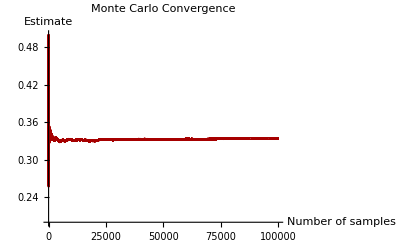

```mathematica
ListLinePlot[estimate,PlotRange->{0.2,0.5},AxesLabel->{"Number of samples","Estimate"},PlotLabel->"Monte Carlo Convergence"]
```

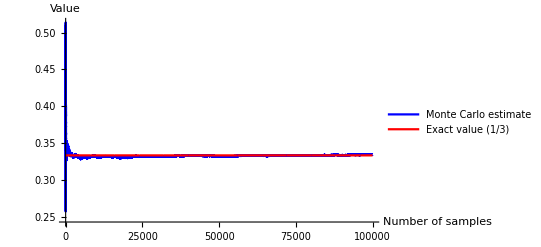

```mathematica
ListLinePlot[{estimate,ConstantArray[1/3,nmax]},PlotStyle->{Blue,Red},PlotRange->All,PlotLegends->{"Monte Carlo estimate","Exact value (1/3)"},AxesLabel->{"Number of samples","Value"}]
```

The error decreases approximately as  error~1/√N.

```mathematica
Accumulate[{1,2,3}]
```

{1,3,6}

Generating and Visualizing Data

We start by generating a sample of 100 measurements for a physical quantity (e.g., the length of a rod) with a known mean and standard deviation.

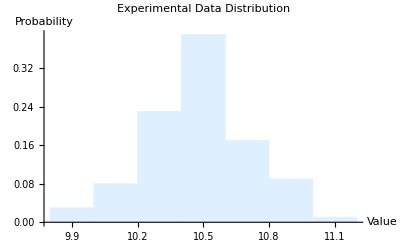

```mathematica
data=RandomVariate[NormalDistribution[10.5,0.2],100];  (* sample data - Gaussian shaped *)

Histogram[data,Automatic,"Probability",ChartStyle->LightBlue,PlotLabel->"Experimental Data Distribution",AxesLabel->{"Value","Probability"}]
```

```mathematica
Mean[data]
StandardDeviation[data]
StandardDeviation[data]/Sqrt[Length[data]]
```

10.4809

0.236384

0.0236384

1.99471 ⅇ^(-12.5 (-10+x)^2)

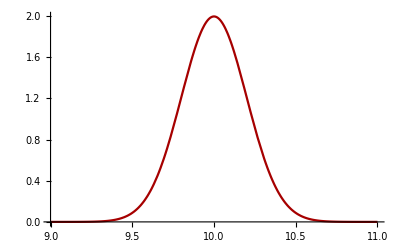

```mathematica
PDF[NormalDistribution[10,0.2],x]
Plot[%,{x,9,11}]
```

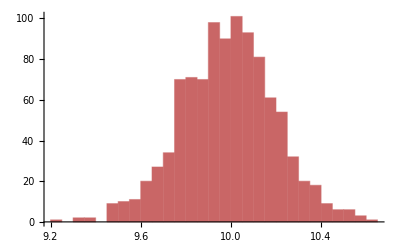

```mathematica
RandomVariate[NormalDistribution[10,0.2],1000]//Histogram
```

Error Bar Plots

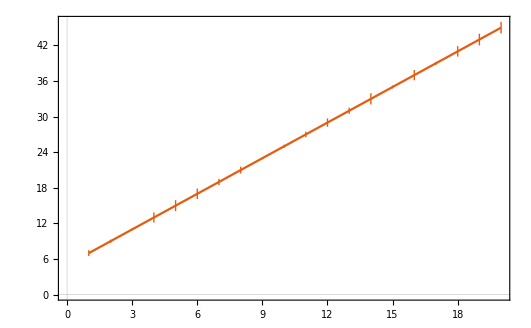

```mathematica
Data=Table[{i,2 i+5+RandomVariate[NormalDistribution[0,2]]},{i,1,20,1}];
DataWithErrors=Table[{i,Around[2 i+5,RandomReal[1]]},{i,1,20}];
ListLinePlot[DataWithErrors,PlotTheme->"Scientific"]
```

```mathematica
RandomReal[1]
```

0.891257

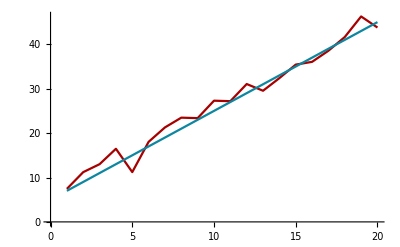

```mathematica
ListLinePlot[{Data,Table[{i,2 i+5},{i,1,20}]}]
```

## 2. Symbolic Error Propagation

We use Mathematica’s symbolic engine to calculate how errors in inputs affect a calculated result.
The uncertainty of a function  F(x_1,x_2,...)  is determined by the partial derivatives of the function with respect to each variable x_i, weighted by their individual uncertainties σ_x_i .

The general formula for uncorrelated variables is:

σ_F=√(∑_i ((δ F)/(δ x_i)σ_x_i)^2)

```mathematica
f[x_,y_]:=x y
```

```mathematica
D[f[x,y],x]
```

y

```mathematica
D[f[x,y],y]
```

x

```mathematica
sigmaf=Sqrt[(D[f[x,y],x] sx)^2+(D[f[x,y],y] sy)^2]
```

√(sy^2 x^2+sx^2 y^2)

```mathematica
PropagateError[func_,vars_List,sigmas_List]:=Sqrt[Total[(D[func,#[[1]]]^2*#[[2]]^2)&/@Transpose[{vars,sigmas}]]];
```

```mathematica
PropagateError[x y,{x,y},{sx,sy}]//Simplify
```

√(sy^2 x^2+sx^2 y^2)

```mathematica
PropagateError[x y z,{x,y,z},{sx,sy,sz}]//Simplify
```

√(sz^2 x^2 y^2+(sy^2 x^2+sx^2 y^2) z^2)

```mathematica
m=xyz
```

xyz

```mathematica
m
```

xyz

```mathematica
Clear[m,r,h,σm,σr,σh]; 
rho=m/(Pi*r^2*h); (*Example: ρ=m/(π r^2 h)*)
```

```mathematica
PropagateError[rho,{m,r,h},{σm,σr,σh}]//Simplify
```

(√((h^2 r^2 σm^2+m^2 (r^2 σh^2+4 h^2 σr^2))/(h^4 r^6)))/π

Let’s say you are measuring the Kinetic Energy (K_E=1/2 m v^2) of an object. You have the mass m and velocity v, both with known uncertainties σ_m and σ_v .

```mathematica
ke=1/2*m*v^2;
keError=PropagateError[ke,{m,v},{σm,σv}]//PowerExpand//Simplify
```

√((v^4 σm^2)/4+m^2 v^2 σv^2)

```mathematica
labValues={m->0.50,v->12.4,σm->0.01,σv->0.2  };  (* in SI units *)
```

```mathematica
ke/.{m->0.5,v->12.4}
```

38.44

```mathematica
√((v^4 σm^2)/4+m^2 v^2 σv^2)/.{m->0.50,v->12.4,σm->0.01,σv->0.2  }
```

1.45899

```mathematica
Print["Calculated KE: ",ke/. labValues," J"];
Print["Uncertainty: ",keError/. labValues," J"];
```

Calculated KE: 38.44 J

Uncertainty: 1.45899 J

In modern Mathematica (12.0+),  the built-in Around object encapsulates a value and its uncertainty. Mathematica will automatically handle the error propagation using first-order Taylor series expansion.

```mathematica
mMeasured=Around[0.50,0.01] (*Around[Subscript[x, 1],Subscript[σ, Subscript[x, 1]]]*)
vMeasured=Around[12.4,0.2]   (*Around[Subscript[x, 2],Subscript[σ, Subscript[x, 2]]]*)
```

0.5000.010

12.400.20

```mathematica
keFinal=1/2*mMeasured*vMeasured^2 (*following standard scientific rounding rule*)
```

38.41.5

Visualization

To see which variable contributes most to your total error, you can plot the error components.

```mathematica
compM=(D[ke,m]*σm)^2;
compV=(D[ke,v]*σv)^2;
```

```mathematica
PieChart[{compM,compV}/. labValues,ChartLabels->{"Mass Contribution","Velocity Contribution"},PlotLabel->"Error Budget Analysis"]
```

-Graphics-

Correlation

If you measure the length and width of a metal plate as it heats up, both measurements will increase together -- then the errors are “correlated”. 

The generalized error propagation formula for a function F(x,y) is:

σ_F=((δ F)/(δ x)σ_x)^2+((δ F)/(δ y)σ_y)^2+ 2 ((δ F)/(δ x)) ((δ F)/(δ y)) σ_(x y) ,

where σ_(x y) is the covariance.

In Mathematica, we represent these relationships using a symmetric matrix:

Σ=(σ_x^2 | σ_(x y)
σ_(x y) | σ_y^2)

```mathematica
vars={x,y};
f=x*y;
covMatrix={{0.1,0.05},{0.05,0.2}};
```

```mathematica
jacobian=D[f,{vars}]
```

{y,x}

```mathematica
propagatedVariance=jacobian.covMatrix.Transpose[jacobian] //Expand
```

0.2 x^2+0.1 x y+0.1 y^2

This is used to estimate the variance of a multivariate function based on the uncertainties of its input variables.

The Around object can also handle correlations, but it requires you to define a MultivariateDistribution or use the VectorAround command. VectorAround is specifically designed to hold a list of values and their associated covariance matrix.

```mathematica
meanValues={10.0,5.0};
valsWithCov=VectorAround[meanValues,covMatrix];
```

```mathematica
valsWithCov[[1]]
```

{10.,5.}

```mathematica
valsWithCov[[2]]
```

{{0.1,0.05},{0.05,0.2}}

```mathematica
area=valsWithCov[[1]]*valsWithCov[[2]] (*Calculate Area*)
```

{{1.,0.5},{0.25,1.}}

Visualizing Correlation: Confidence Ellipses

To see how variables are correlated in your data analysis, you can plot a confidence ellipse. If the ellipse is tilted, the variables are correlated.

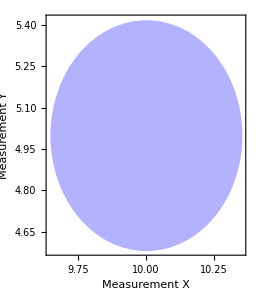

```mathematica
Graphics[{Opacity[0.3],Blue,ConfidenceLevel->0.95,Ellipsoid[meanValues,covMatrix]},Axes->True,Frame->True,FrameLabel->{"Measurement X","Measurement Y"}]
```

Monte Carlo simulation for error propagation

Instead of using calculus (derivatives) or the Around object, we performing an experiment 100,000 times to see how the distribution of the result F(x,y) behaves.

```mathematica
Quit[];
```

```mathematica
f[x_,y_]:=x y;
```

```mathematica
samples=Table[f[RandomVariate[NormalDistribution[0.50,0.01]],RandomVariate[NormalDistribution[12.4,0.2]]],{10^5}];
```

6.19954

0.15912

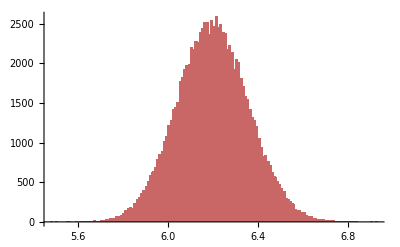

```mathematica
Mean[samples]
StandardDeviation[samples]
Histogram[samples,100]
```

If your function was highly non-linear (e.g., F(x,y) = e^(x/y)), the standard error formula might be slightly wrong ( because Around object uses a linear approximation -- first-order Taylor expansion), while Monte Carlo handles "curved" error spaces perfectly and is exact.

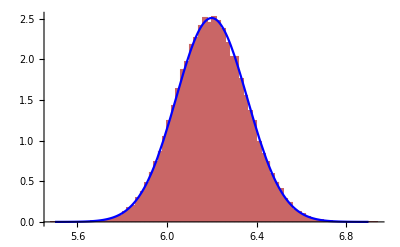

```mathematica
hist=Histogram[samples,50,"PDF"]; (* Comparing to the "Exact" analytic result *)
distPlot=Plot[PDF[NormalDistribution[Mean[samples],StandardDeviation[samples]],x],{x,5.5,6.9},PlotStyle->Blue];

Show[hist,distPlot]
```

Correlated Errors

```mathematica
dist=MultinormalDistribution[{0,0},{{1,0.8},{0.8,1}}];
```

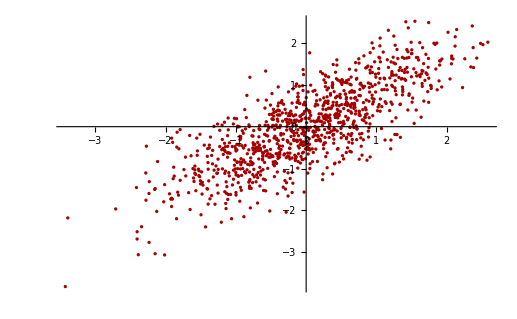

```mathematica
RandomVariate[dist,1000]//ListPlot
```

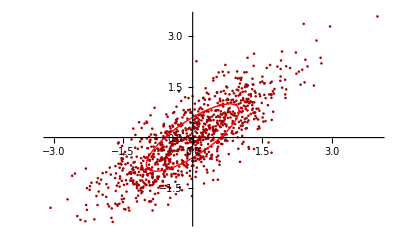

```mathematica
Show[RandomVariate[dist, 1000] // ListPlot, RegionPlot[RegionMember[Ellipsoid[{0, 0}, {{1, 0.8}, {0.8, 1}}], {x, y}], {x, -4, 4}, {y, -4, 4}, PlotStyle -> Transparent, BoundaryStyle -> {Thick, Red}]]
```

```mathematica
cov={{1,0.8},{0.8,1}};  (*Define Covariance Matrix*)
{values,vectors}=Eigensystem[cov];
```

Note: (i) Eigenvectors : direction the ellipse point.
          (ii) Eigenvalues : how long the ellipse is in those directions.

```mathematica
axis1=2*Sqrt[values[[1]]]*vectors[[1]];
axis2=2*Sqrt[values[[2]]]*vectors[[2]];
```

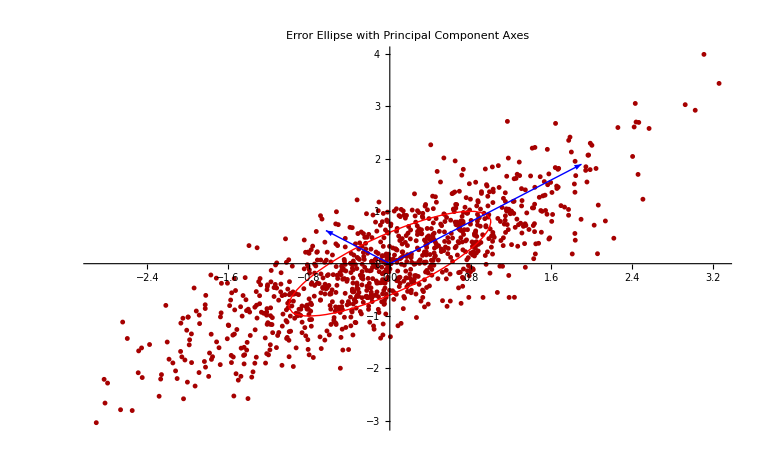

```mathematica
Show[RandomVariate[dist, 1000] // ListPlot, RegionPlot[RegionMember[Ellipsoid[{0, 0}, {{1, 0.8}, {0.8, 1}}], {x, y}], {x, -4, 4}, {y, -4, 4}, PlotStyle -> Transparent, BoundaryStyle -> {Thick, Red}],Graphics[{Thick,Blue,Arrow[{{0,0},axis1}],Arrow[{{0,0},axis2}]}],PlotLabel->"Error Ellipse with Principal Component Axes"
]
```

The Major Axis (Long Arrow): This is the direction of the maximum variance. It represents the primary trend in the data.

The Minor Axis (Short Arrow): This is the direction of minimum variance. It represents the "noise" or the thickness of the correlation.

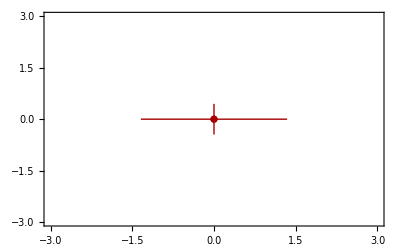

```mathematica
mean={0,0};
covariance={{1,0.8},{0.8,1}};
va=VectorAround[mean,covariance]; (*Using VectorAround for instant visualization*)
ListPlot[{va},PlotRange->{{-3,3},{-3,3}},Frame->True]
```

In Mathematica, the Manipulate command allows us to change the off-diagonal elements of the covariance matrix dynamically.

```mathematica
Manipulate[Module[{cov,vals,vecs,axis1,axis2,dist,pts},
cov={{1,rho},{rho,1}};
{values,vectors}=Eigensystem[cov];
axis1=2*Sqrt[Abs[values[[1]]]]*vectors[[1]];
axis2=2*Sqrt[Abs[values[[2]]]]*vectors[[2]];
SeedRandom[123];dist=MultinormalDistribution[{0,0},cov];
pts=RandomVariate[dist,600];
Show[ListPlot[pts,PlotStyle->Directive[PointSize[Small],Opacity[0.3]],PlotRange->{{-4,4},{-4,4}},Frame->True,AspectRatio->1],RegionPlot[RegionMember[Ellipsoid[{0,0},cov],{x,y}],{x,-4,4},{y,-4,4},PlotStyle->Transparent,BoundaryStyle->{Thick,Red}],Graphics[{Thick,Blue,Arrow[{{0,0},axis1}],Arrow[{{0,0},axis2}]}],PlotLabel->Style["Correlation (ρ) = "<>ToString[rho],14]]],{{rho,0.8,"Correlation (ρ)"},-0.99,0.99,Appearance->"Labeled"}] (*Control:rho ranges from -0.99 to 0.99 to avoid singular matrices*)
```

The "Error" on the fit is essentially the length of that Minor Axis. If the minor axis is very short compared to the major axis, the fit is "good".

Problem-1:

In a resonance tube experiment to measure the speed of sound in air (v_s), a student collected the following set of measurements (in m/s). Due to the nature of the equipment, several measurements were repeated multiple times:
338.0	8
340.0	12
341.5	25
343.0	35
344.5	10
346.0	10

Which of the following is a good estimate (including the error bar) for the speed of sound v_s, based on this experimental data?

We use the ConstantArray and Flatten functions to build the full list of 100 data points (reconstruct the data).

```mathematica
Quit[];
```

```mathematica
values={338.0,340.0,341.5,343.0,344.5,346.0};
freqs={8,12,25,35,10,10};
```

```mathematica
Data=Flatten[MapThread[ConstantArray,{values,freqs}]]; (*Build the full dataset*)
n=Length[Data];
```

```mathematica
n
```

100

```mathematica
meanVs=Mean[Data]
sdVs=StandardDeviation[Data]*(Sqrt[Length[Data]-1]/Sqrt[Length[Data]])
semVs=sdVs/Sqrt[n] (* error-bar *)
```

342.315

2.07323

0.207323

```mathematica
Around[meanVs,semVs]
```

342.320.21

## 3. Curve Fitting and Parameter Estimation

We want to extract physical constants (e.g., G or k) from noisy experimental data.

Linear Fit

```mathematica
ClearAll[x]
data=Table[{x,2 x+1+RandomVariate[NormalDistribution[0,0.5]]},{x,0,10,1}];
```

```mathematica
ListPlot[data]
```

To fit a model of the form a x+b :

```mathematica
Lm=LinearModelFit[data,{x,1},x];
Lm["BestFitParameters"] (* best fit value of {a,b} *)
```

{1.92501,1.44099}

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[Lm[x],{x,Min[data[[All,1]]],Max[data[[All,1]]]}]]
```

Parameter Errors and Covariance Matrix:

```mathematica
Lm["ParameterErrors"]
Lm["CovarianceMatrix"]
```

Ex-1: Let’s generate pseudo data that mimics a real experiment, such as a falling object (v=v_0+g t).

```mathematica
v0=2.5;
g=9.8;
data=Table[{t,v0+g*t+RandomReal[{-1,1}]},{t,0,5,0.5}];
```

```mathematica
Lm=LinearModelFit[data,{1,t},t]; (* Perform the fit *)
Lm["BestFitParameters"] (* Returns {v0,g}*)
Lm["ParameterTable"]
```

{2.3696,9.87677}

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.3696 | 0.174398 | 13.5873 | 2.65506×10^-7
t | 9.87677 | 0.0589574 | 167.524 | 4.8934×10^-17

Note: (i)  t==(Estimated Value)/(Standard Error) (signal-to-noise ratio) , high t-statistic suggest that the effect is real.

(ii) p-value -- represents the probability that you would see your result if the true parameter value was actually zero (the "null hypothesis"). A small p-value means your parameter is “statistically significant”.

Most physics models (e.g., radioactive decay) are nonlinear.

```mathematica
NLm=NonlinearModelFit[data,a*x+b,{a,b},x];
NLm["BestFitParameters"]
```

Ex-2: Radioactive Decay, N(t)=N_0 e^(-λ t) :

```mathematica
decayData=Table[{t,100*Exp[-0.5*t]+RandomReal[{-2,2}]},{t,0,10,1}];
```

```mathematica
NLm=NonlinearModelFit[decayData,n0*Exp[-lambda*t],{n0,lambda},t]; (*Fit the model*)
```

```mathematica
Plot[NLm[t],{t,0,10},Epilog->{Red,PointSize[Medium],Point[decayData]},PlotLabel->"Radioactive Decay Fit"]  (*Visualize the fit*)
```

Error Analysis & Goodness of Fit

```mathematica
v0=2.5;
g=9.8;
data=Table[{t,v0*1+g*t+RandomReal[{-1,1}]},{t,0,5,0.5}];
```

```mathematica
Lm=LinearModelFit[data,{1,t},t]; (* Perform the fit *)
Lm["BestFitParameters"] (* Returns {v0,g}*)
Lm["ParameterTable"]
```

{2.83597,9.78528}

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.83597 | 0.382938 | 7.4058 | 0.0000407827
t | 9.78528 | 0.129457 | 75.5872 | 6.28115×10^-14

A residual is the difference between the observed data and the model's prediction. If the residuals look like random dots around the zero line, then the model is likely correct.

```mathematica
ListPlot[Lm["FitResiduals"],Filling->Axis,PlotStyle->Red,PlotLabel->"Residual Analysis"]
```

(i) ParameterErrors -- standard deviation of the parameter estimate.
(ii) ConfidenceIntervals -- the 95% range where the true physical value likely resides.

```mathematica
Lm[{"BestFitParameters","ParameterErrors","ParameterConfidenceIntervals"}]
```

Ex-3:

```mathematica
b=2.0;
a=5.0;
SeedRandom[42];
data=Table[{x,a*x+b+RandomVariate[NormalDistribution[0,4]]},{x,1,20}];
ListPlot[data,PlotStyle->Red,PlotLabel->"Scattered  Data"]
```

```mathematica
Lm=LinearModelFit[data,{1,x},x];

slopeValue=Lm["BestFitParameters"][[2]];
slopeError=Lm["ParameterErrors"][[2]];

Print["Estimated Slope: ",slopeValue];
Print["Uncertainty (Error): ",slopeError];
```

```mathematica
tStat=slopeValue/slopeError;
Print["t-Statistic: ",tStat]
```

```mathematica
Show[ListPlot[data,PlotStyle->{Red,PointSize[Medium]}],Plot[{Lm[x],Lm["MeanPredictionBands"]},{x,0,20},PlotStyle->{Blue,{Dashed,Gray},{Dashed,Gray}},PlotLegends->{"Best Fit","95% Confidence"}]]
```

"Goodness of Fit" -- the quantitative way to answer the question: "How much should I trust this model?".

χ_ν^2==1/(d.o.f)∑(y_obs-y_fit)^2/σ_error^2   (Reduced Chi-Squared)

```mathematica
b=2.0;
a=5.0;
SeedRandom[42]; (* initialize the pseudo-random number generator *)
data=Table[{x,a*x+b+RandomVariate[NormalDistribution[0,4]]},{x,1,20}];
ListPlot[data,PlotStyle->Red,PlotLabel->"Scattered  Data"]
```

```mathematica
Lm=LinearModelFit[data,{1,x},x];
```

```mathematica
sigmaError=4.0;
estVar=Lm["EstimatedVariance"];
reducedChiSq=estVar/(sigmaError^2)  (*Calculate Reduced Chi-Squared*)
```

Problem-2:
Generate a table of n random numbers using the RandomReal[{-1, 1}] function (note that these numbers are centered at zero). Calculate the Standard Deviation of these n numbers. Repeat this process for n running from 100 to 2000 in steps of 200.

Fit the result to the power-law form:

f(n)==a·n^b

Q. What value is the exponent b closest to ?

```mathematica
ClearAll[a,b,n]
```

```mathematica
data=Table[{n,StandardDeviation[RandomReal[{-1,1},n]]},{n,100,2000,200}];
NLm=NonlinearModelFit[data,a*n^b,{a,b},n];
Print["Best Fit Parameters: ",NLm["BestFitParameters"]];
Print["Parameter Table:"];
NLm["ParameterTable"]
```

Best Fit Parameters: {a→0.523654,b→0.0150457}

Parameter Table:

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.523654 | 0.0225104 | 23.2628 | 1.23873×10^-8
b | 0.0150457 | 0.00640407 | 2.3494 | 0.0467251